Ryan Foundoulis
605107291
ryanfoundoulis@gmail.com
HW 1

My CS experience is relatively limited. I have a bit of experience in Python from self teaching and what we had learned in 4AL. I also have experience in C++ from CS31 and feel that I have a pretty good command of all that we had learned in that class. I have not used Mathematica, MatLab, or anything similar in the past.

```mathematica
(* Problem 3 *)
a=16;
b= 0.25;
ab = 22;
a b
ab
ab/(a b)
"I have not figured out the best way to get my explanation formatted below the results of the operation so this is how I will do it for now. The first three outputs are simply showing that we have defined varaibles a, b, ab with there respective values. The command a b seems to be multiplying variables a and b together for a result of 4, ab simply calls the value stored in ab, and ab/(a b) divides ab by the value of a and b multiplied (4.)"
```

4.

22

5.5

I have not figured out the best way to get my explanation formatted below the results of the operation so this is how I will do it for now. The first three outputs are simply showing that we have defined varaibles a, b, ab with there respective values. The command a b seems to be multiplying variables a and b together for a result of 4, ab simply calls the value stored in ab, and ab/(a b) divides ab by the value of a and b multiplied (4.)

```mathematica
(* Problem 4 *)
Clear["Global`*"]
540a^4-1017a^3b-834a^2b^2+653a b^3-70b^4  //Factor
```

(3 a-7 b) (12 a-5 b) (15 a-2 b) (a+b)

```mathematica
(* Problem 5 *)
Clear["Global`*"]
f[θ,ϕ] =(Sin[θ]*Cos[ϕ]+Sin[ϕ]*Cos[θ]) //Simplify
g[θ,ϕ] = Sin[θ+ϕ]

(* Trying through comparing direct Eqs
(Sin[θ]*Cos[ϕ]+Sin[ϕ]*Cos[θ]) == Sin[θ+ϕ] *)

f[θ,ϕ]== g[θ,ϕ]
```

Sin[θ+ϕ]

Sin[θ+ϕ]

True

```mathematica
(* Problem 6 *)
Clear["Global`*"]
f =(6.35^(1/5)-12.6(2.6*10^7)^(1/4))/(7.6*10^-5)^3; ScientificForm[f,4]
```

-2.046×10^15

```mathematica
(* Problem 7 *)
Clear["Global`*"]
a = -1.5*10^-7;b = 5*10^9;c = -500;
x[t_] = c+b t+a t^2


	(* i) *) "i)"
         t1 =((-b-Sqrt[(b^2)-4(a c)])/(2a))
         t2 = c/(t1 * a)
	
	(* ii) *) "ii)"

	(* Finding the values of x at each time t *)
	t = 0; x0 = x[t]
	t = t1; x1 =x [t]
	t = t2; x2 = x[t]

  "The value given above, while not being zero, approaches zero to a very close degree. I believe it has to do with the finite value of exactness that is given by t2 to be plugged into x[t]."
	
	(* Finding average Velocities from given Eq *)
	"Average Velocities"
	aveVel1 = (x1 - x0)/(t1) 
	aveVel2 = (x2 - x0)/(t2)

	"These two values give us such different values for average velocities due to the fact of the difference in time that is used for each one. Our value for t1, being on the order of 10^16 give more of an average value where our t2 is on the order of 10^-7, making it much more of an instantaneous velocity between time zero and time 1.*10^-7"
	
	(* iii) *) "iii)" 

"Evaluation of average velocity between the roots (i.e. should be 0 or close to zero)."

	aveVel3 = (x1 - x2) / (t1 - t2)

"It is hard to define what a good evaluation of an average velocity would be, since whatever times we choose to evaluate can change the outcome dramatially, seen in the three average velocities computed above."
```

-500+5000000000 t-1.5×10^-7 t^2

i)

3.33333×10^16

1.×10^-7

ii)

-500.

0.

5.68434×10^-14

The value given above, while not being zero, approaches zero to a very close degree. I believe it has to do with the finite value of exactness that is given by t2 to be plugged into x[t].

Average Velocities

1.5×10^-14

5.×10^9

These two values give us such different values for average velocities due to the fact of the difference in time that is used for each one. Our value for t1, being on the order of 10^16 give more of an average value where our t2 is on the order of 10^-7, making it much more of an instantaneous velocity between time zero and time 1.*10^-7

iii)

Evaluation of average velocity between the roots (i.e. should be 0 or close to zero).

-1.7053×10^-30

It is hard to define what a good evaluation of an average velocity would be, since whatever times we choose to evaluate can change the outcome dramatially, seen in the three average velocities computed above.

```mathematica
(* Problem 8 *)
Clear["Global`*"]
A = {{s,u,v},{d,e,f},{g,h,i}};
B = {{j,k,l},{m,n,o},{p,q,r}};

	A // MatrixForm
	B // MatrixForm

(*Examples with Numbers:
	 A  = {{7,2,1},{0,3,-1},{-3,4,-2}};
          B  = {{-2,3,9},{8,-11,-34},{-5,7,21}}; *)

	(* i) *) "i)"
	
	Transpose[A.B] ==  Transpose[B].Transpose[A]

	(* ii) *) "ii)"

	Y = A.B //FullSimplify;
	T = Inverse[Y] // FullSimplify;
	X = Inverse[B] //FullSimplify;
	P = Inverse[A] //FullSimplify;
	T == X.P//FullSimplify
```

(s | u | v
d | e | f
g | h | i)

(j | k | l
m | n | o
p | q | r)

i)

True

ii)

True

{-Cos[t]+t (-Sin[t]+Sin[π/6+t]),-t Cos[t]+t Cos[π/6+t]+Sin[t]}

i)

{-t Cos[t]+t Cos[π/6+t]+Sin[π/6+t],Cos[π/6+t]+t (Sin[t]-Sin[π/6+t])}

{-Cos[t]+2 Cos[π/6+t]+t (Sin[t]-Sin[π/6+t]),t Cos[t]-t Cos[π/6+t]+Sin[t]-2 Sin[π/6+t]}

(1-t (1+(-2+√3) t))^0.5

ii)

ArcCos[√(317/1924+(20 √3)/481)]

iii)

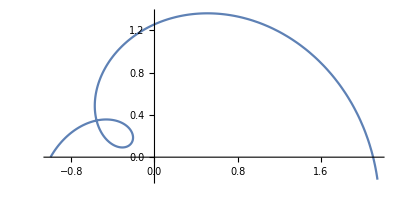

```mathematica
(* Problem 9 *)
Clear["Global`*"]
xPos[t_] = t*Sin[t+Pi/6]-t*Sin[t]-Cos[t] // FullSimplify;
yPos [t_]= Sin[t]-t*Cos[t]+t*Cos[t+Pi/6] // FullSimplify;
r = {xPos[t],yPos[t]} 

	(* i) *) "i)"
	(* Derivatives of each position component and insert into a velocity vector*)
	xVel[t_] = D[xPos[t],t];
	yVel[t_] = D[yPos[t],t];
	v = {xVel[t],yVel[t]} //FullSimplify
	

	(* Find Accelerations *)
	xAcc[t_] = D[xVel[t], t]//FullSimplify;
	yAcc[t_] = D[yVel[t], t]//FullSimplify;
	a = {xAcc[t], yAcc[t]} 

	(* Speed of Particle *)
	speed = (xVel[t]^2 + yVel[t]^2)^.5 //FullSimplify

	(* ii) *) "ii)"
	angle[t_] = ArcCos[(v.a)/(Norm[a] Norm[v])] ;
	FullSimplify[angle[t] /. t-> 3 ]
	
	
	(* iii) *) "iii)"
	ParametricPlot[{t Sin[t+Pi/6]-t Sin[t]-Cos[t],Sin[t]-t Cos[t]+t Cos[t+Pi/6]}, {t,0,6}]
```

```mathematica
DSolve[x''[t]+k x'[t]^2 - g Sin[θ] == 0, x[t], t]
```

{{x[t]→C[2]+Log[Cosh[√g √k (t-C[1]) √Sin[θ]]]/k}}